# NCSE Usage Notebook

This notebook shows how to use the NCSE package for NCAlgebra. NCSE is a package designed for performing optimization over free spectrahedra. The package contains tools for optimizing linear functions on a free spectrahedron, finding extreme points of free spectrahedra, and classifying extreme points as free or classical extreme. Additionally, the package contains commands for dilating a given tuple to a Arveson (free) extreme point. Several other utilities for working on free spectrahedra are included. 

Note: Several functions in NCSE use Mathematica’s SDP for semidefinite optimization by default. With default settings these functions require Mathematica 12.0 or later to run.

## Initialization of NCSE and beginner notebook.

## Required packages

The following packages are required for NCSE to work.

```mathematica
<<NC`
<<NCSE`
```

You are using the version of NCAlgebra which is found in:

C:\Users\ericm\NC\

You can now use "<< NCAlgebra`" to load NCAlgebra.

## Optional packages

The following packages are optional. 

SDP calls the NCSDP package. Older versions of NCSE used the NCSDP Semidefinite program to optimization. After the addition of Mathematica’s semidefinite program in Mathematica 12, NCSE has been updated to use the Mathematica solver by default, as it is much faster. As an option, the user may instead use the NCSDP.

NCSEBackwardsCompatible is used to make the current version of NCSE compatible with old notebooks made in NCSE. The names of several NCSE functions were updated in August 2018. Notebooks made before then and other notebooks using old function names will require NCSEBackwardsCompatible to run.

```mathematica
<<SDP`
<<NCSEBackwardsCompatible`
```

## Variables used in the NCSEBeginner notebook

This section contains many of the variables used in the NCSEBeginner notebook. This section needs to be be evaluated if the user is only using specific sections of this notebook to ensure that all necessary variables are defined.

```mathematica
X1={{{1}},{{1}}};
X2={{{2,3},{3,4}},{{-6,5},{5,-4}}};
X3=RandomReal[{},{2,3,3}];
X4=RandomReal[{},{3,2,2}];
X5={DiagonalMatrix[{3,2,1}],DiagonalMatrix[{1,2,6}]};
M={{2,3},{3,4}};

circ={{{0,1},{1,0}},{{1,0},{0,-1}}};
square={DiagonalMatrix[{1,-1,0,0}],DiagonalMatrix[{0,0,1,-1}]};
sphere1={{0,1,0,0},{1,0,0,0},{0,0,0,0},{0,0,0,0}};
sphere2={{0,0,1,0},{0,0,0,0},{1,0,0,0},{0,0,0,0}};
sphere3={{0,0,0,1},{0,0,0,0},{0,0,0,0},{1,0,0,0}};
sphere={sphere1,sphere2,sphere3};
apent={DiagonalMatrix[{1,-1,0,0,1}],DiagonalMatrix[{0,0,1,-1,1}]};

Ag3d4=MakeBoundedA[3,4,100];
Ag4d5=MakeBoundedA[4,5,3];
```

## Basics of working with Linear pencils and free spectrahedra in NCSE

## Basic computations with matrix tuples

The NCSE package is designed for working with tuples of matrices. Several basic functions for working with matrix tuples are included. In the following explanation of functions, X will always represent a tuple of matrices while M is a single matrix.

1. ViewTuple[X] shows each entry of the matrix tuple X in matrix form

```mathematica
X1={{{1}},{{1}}};
X2={{{2,3},{3,4}},{{-6,5},{5,-4}}};
X3=RandomReal[{},{2,3,3}];
X4=RandomReal[{},{3,2,2}];
ViewTuple[X1]
ViewTuple[X2]
ViewTuple[X3]
ViewTuple[X4]
```

{(1),(1)}

{(2 | 3
3 | 4),(-6 | 5
5 | -4)}

{(0.133721 | 0.348832 | 0.182328
0.648071 | 0.369534 | 0.664786
0.230951 | 0.558482 | 0.804608),(0.0307942 | 0.459123 | 0.531943
0.540745 | 0.331184 | 0.576213
0.593371 | 0.371837 | 0.541511)}

{(0.600545 | 0.124903
0.38568 | 0.195434),(0.430073 | 0.914485
0.113014 | 0.997252),(0.896421 | 0.558805
0.832162 | 0.0232145)}

2. DirectSumTuple[TupleList] computes the direct sum of a list of matrix tuples given in TupleList.

```mathematica
ViewTuple[DirectSumTuple[{X1,X2}]]
ViewTuple[DirectSumTuple[{X3,X1,X2}]]
```

{(1 | 0 | 0
0 | 2 | 3
0 | 3 | 4),(1 | 0 | 0
0 | -6 | 5
0 | 5 | -4)}

{(0.133721 | 0.348832 | 0.182328 | 0 | 0 | 0
0.648071 | 0.369534 | 0.664786 | 0 | 0 | 0
0.230951 | 0.558482 | 0.804608 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 2 | 3
0 | 0 | 0 | 0 | 3 | 4),(0.0307942 | 0.459123 | 0.531943 | 0 | 0 | 0
0.540745 | 0.331184 | 0.576213 | 0 | 0 | 0
0.593371 | 0.371837 | 0.541511 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | -6 | 5
0 | 0 | 0 | 0 | 5 | -4)}

3. TupleNorm[X] computes the norm of the matrix tuple X. Here the norm of the tuple A is defined as ||A||=[tuple_]:=Sqrt[Norm[Sum[tuple[[i]]^2,{i,Length[tuple]}]]]

```mathematica
TupleNorm[X1]
TupleNorm[X2]
```

√2

√2 (617+36 √293)^(1/4)

4. LeftMultTuple[M,X] left multiplies each entry of the matrix tuple X by the matrix M
5. RightMultTuple[M,X] right multiplies each entry of the matrix tuple X by the matrix M
6. ConjTuple[M,X] conjugates each entry of the matrix tuple X by the matrix M. That is each entry of X is left multiplied by Tranpose[M] and right multipled by M.
7. TupleComm[M,X] computes the commutant of the tuple X with M. That is, for each entry of X, TupleComm computes M.X[[i]]-X[[i]].M

```mathematica
M={{2,3},{3,4}};
ViewTuple[LeftMultTuple[M,X2]]
ViewTuple[RightMultTuple[M,X2]]
ViewTuple[ConjTuple[M,X2]]
ViewTuple[TupleComm[M,X2]]
```

{(13 | 18
18 | 25),(3 | -2
2 | -1)}

{(13 | 18
18 | 25),(3 | 2
-2 | -1)}

{(80 | 111
111 | 154),(0 | 1
1 | 2)}

{(0 | 0
0 | 0),(0 | -4
4 | 0)}

8. CommutantDimension[X] computes the dimension of the space of real symmetric tuples M which satisfy M.X[[i]]-X[[i]].M=0 for all i. The first output is the dimension of the commutant. The second output is a numerical tolerance for the computation. Smaller is better here. If the dimension of the commutant is 1 then the tuple is irreducible over the real. Otherwise it is reducible over the reals.

```mathematica
CommutantDimension[X2]
```

{1,6.05737×10^-23}

```mathematica
X5={DiagonalMatrix[{3,2,1}],DiagonalMatrix[{1,2,6}]};
CommutantDimension[X5]
```

{3,0.}

## Representing free spectrahedra and linear pencils in NCSE

In NCSE, Linear pencils and free spectrahedra are defined by tuples of matrices. For example “circ” below is a matrix tuple which defines a free disc in two variables, “sqruare” defines a free square in two variables, and “sphere” defines a free disc in three variables.

ViewLMIGraphic shows the monic linear pencil defined by circ.

```mathematica
circ={{{0,1},{1,0}},{{1,0},{0,-1}}};
square={DiagonalMatrix[{1,-1,0,0}],DiagonalMatrix[{0,0,1,-1}]};
sphere1={{0,1,0,0},{1,0,0,0},{0,0,0,0},{0,0,0,0}};
sphere2={{0,0,1,0},{0,0,0,0},{1,0,0,0},{0,0,0,0}};
sphere3={{0,0,0,1},{0,0,0,0},{0,0,0,0},{1,0,0,0}};
sphere={sphere1,sphere2,sphere3};
ViewLMIGraphic[circ]
ViewLMIGraphic[square]
ViewLMIGraphic[sphere]
```

(1-X[2] | -X[1]
-X[1] | 1+X[2])

(1-X[1] | 0 | 0 | 0
0 | 1+X[1] | 0 | 0
0 | 0 | 1-X[2] | 0
0 | 0 | 0 | 1+X[2])

(1 | -X[1] | -X[2] | -X[3]
-X[1] | 1 | 0 | 0
-X[2] | 0 | 1 | 0
-X[3] | 0 | 0 | 1)

## Evaluating Linear pencils on matrix variables

LMI[A,X] evaluates the monic linear pencil defined by A on the matrix tuple X. 
Lambda[A,X] evaluates the linear pencil defined by A on the matrix tuple X. In the convention used in NCSE, one has LMI[A,X]= I-Lambda[A,X].

```mathematica
X2={{{2,3},{3,4}},{{-6,5},{5,-4}}};
ViewTuple[X2]
LMI[circ,X2]
Lambda[circ,X2]
IdentityMatrix[4]-Lambda[circ,X2]==LMI[circ,X2]
```

{(2 | 3
3 | 4),(-6 | 5
5 | -4)}

{{7,-5,-2,-3},{-5,5,-3,-4},{-2,-3,-5,5},{-3,-4,5,-3}}

{{-6,5,2,3},{5,-4,3,4},{2,3,6,-5},{3,4,-5,4}}

True

## Checking Spectrahedron membership

The matrix tuple X is an element of the free spectrahedron defined by A if LMI[A,X] is positive semidefinite. One may use PositiveSemidefiniteMatrixQ to check this.
PencilEig[A,X] is computes the eigenvalues of LMI[A,X].
X is not a member the free spectrahedron defined by circ. However X/100 is a member.

```mathematica
PositiveSemidefiniteMatrixQ[LMI[circ,X2]]
PencilEig[circ,X2]//N
PositiveSemidefiniteMatrixQ[LMI[circ,X2/100]]
PencilEig[circ,X2/100]//N
```

False

{11.124,-9.12404,7.12404,-5.12404}

True

{1.10124,1.06124,0.93876,0.89876}

## Generating random free spectrahedra

A bounded free spectrahedron may be randomly generated using the MakeBoundedA command. MakeBoundedA[g,d,seed] randomly (using the given seed) generates a g tuple A of d x d matrices which defines a bounded free spectrahedron.

```mathematica
Ag3d4=MakeBoundedA[3,4,100];
ViewTuple[Ag3d4]
Ag4d5=MakeBoundedA[4,5,3];
ViewTuple[Ag4d5]
```

{(-5 | 1 | 23/10 | -7/10
1 | 11/5 | 3/5 | -3/10
23/10 | 3/5 | 4/5 | 14/5
-7/10 | -3/10 | 14/5 | 11/5),(12/5 | 5/2 | 11/10 | 11/5
5/2 | 1 | -9/10 | -11/10
11/10 | -9/10 | -4/5 | -9/5
11/5 | -11/10 | -9/5 | 17/5),(-4 | -33/10 | 13/5 | 0
-33/10 | -6/5 | -19/10 | -3/2
13/5 | -19/10 | 9/5 | 33/10
0 | -3/2 | 33/10 | -23/5)}

{(1 | 16/5 | -8/5 | -3/2 | 3
16/5 | -8/5 | -7/2 | -7/5 | -11/10
-8/5 | -7/2 | -6/5 | 9/5 | 27/10
-3/2 | -7/5 | 9/5 | -16/5 | -7/5
3 | -11/10 | 27/10 | -7/5 | 22/5),(21/5 | 6/5 | -17/10 | 0 | 1/2
6/5 | 16/5 | -11/5 | -1 | -12/5
-17/10 | -11/5 | 13/5 | -3/10 | 13/5
0 | -1 | -3/10 | -22/5 | 4/5
1/2 | -12/5 | 13/5 | 4/5 | -16/5),(21/5 | -19/5 | -19/10 | -9/10 | -2/5
-19/5 | -18/5 | 13/5 | -13/5 | 4
-19/10 | 13/5 | 2/5 | -1/10 | 13/5
-9/10 | -13/5 | -1/10 | 4/5 | -1/10
-2/5 | 4 | 13/5 | -1/10 | 7/5),(11/5 | -1 | 11/10 | -16/5 | -13/10
-1 | 7/5 | -12/5 | -9/10 | 1/5
11/10 | -12/5 | -21/5 | -7/10 | -7/10
-16/5 | -9/10 | -7/10 | -5 | -19/10
-13/10 | 1/5 | -7/10 | -19/10 | -1/5)}

## Visualization of spectrahedra

Level1ExtremePlot may be used to visualize free spectrahedra in 2,3 or 4 variables. This function which randomly generates then plots extreme points at level 1 of the specified free spectrahedron.

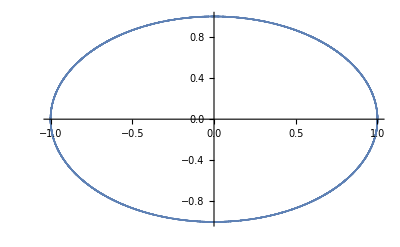

```mathematica
Level1ExtremePlot[circ]
```

```mathematica
Level1ExtremePlot[sphere]
```

-Graphics3D-

```mathematica
Level1ExtremePlot[Ag4d5]
```

-Graphics3D-

By default Level1ExtremePlot randomly generates 10000 points. The user may increase this value to create denser images the cost of run time, or may decrease this to improve run time. This is particularly useful when working with a polyhedron.

```mathematica
Level1ExtremePlot[sphere,PointCount-> 100000]
```

-Graphics3D-

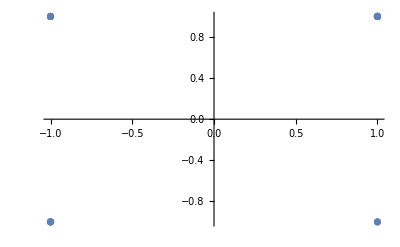

```mathematica
Level1ExtremePlot[square,PointCount-> 20]
```

## Generation and classification of extreme points of free spectrahedra

## Generation of Extreme points using FindExtremePoint

The main command for generating extreme points in NCSE is FindExtremePoint. FindExtremePoint[A,n] generates an extreme point at level n of the free spectrahedron defined by the tuple A by randomly generating then optimizing a linear functional at level n. By default FindExtremePoint also computes various information about the extreme point. The amount of information generated can be changed by changing the DiagnosticLevel option for FindExtremePoint.  At first we heavily limit the amount of Diagnostic information generated.

As before, we will work with a free disc in two variables .

```mathematica
circ={{{0,1},{1,0}},{{1,0},{0,-1}}};
```

With DiagnosticLevel→0 the output of FindExtremePoint is simply the optimizer of the randomly generated linear functional.

```mathematica
circExtremePoint1=FindExtremePoint[circ,1,DiagnosticLevel->0];
circExtremePoint2=FindExtremePoint[circ,2,DiagnosticLevel->0];
ViewTuple[circExtremePoint1]
ViewTuple[circExtremePoint2]
```

{(-0.186541),(0.982447)}

{(-0.924749 | -0.218617
-0.218617 | 0.970943),(0.308187 | 0.0454676
0.0454676 | -0.086076)}

One can check that the level one extreme points of circ have norm 1.

```mathematica
TupleNorm[circExtremePoint1]
```

1.

The user may specify the linear functional optimized by giving a WeightVector. For example the WeightVector {1,0} corresponds to minimizing X[[1]]+0*X[[2]].

```mathematica
circExtremePoint3=FindExtremePoint[circ,1,DiagnosticLevel->0,WeightVector-> {1,0}];
ViewTuple[circExtremePoint3]
```

{(-1.),(-8.46678×10^-12)}

If DiagnosticLevel is greater than 0, then as a second output, FindExtremePoint will return the WeightVector for the linear functional that was optimized to produce the given tuple. This allows reproducibility of results.

```mathematica
{circExtremePoint4,functionalWeight}=FindExtremePoint[circ,3,DiagnosticLevel-> 1];
ViewTuple[circExtremePoint4]
circExtremePointTest=FindExtremePoint[circ,3,DiagnosticLevel-> 0,WeightVector-> functionalWeight];
ViewTuple[circExtremePointTest]
```

{(0.673551 | 0.0122158 | -0.066061
0.0122158 | 0.758599 | -0.186827
-0.066061 | -0.186827 | -0.977623),(0.69595 | -0.239723 | -0.00127012
-0.239723 | -0.571861 | 0.0705898
-0.00127012 | 0.0705898 | -0.000704156)}

{(0.673551 | 0.0122158 | -0.066061
0.0122158 | 0.758599 | -0.186827
-0.066061 | -0.186827 | -0.977623),(0.69595 | -0.239723 | -0.00127012
-0.239723 | -0.571861 | 0.0705898
-0.00127012 | 0.0705898 | -0.000704156)}

The linear functional used can be viewed by using MakeFunctionalRational.

```mathematica
MakeFunctionalRational[2,3,WeightVector->functionalWeight]
```

{{-151/100,-37/50,-7/100,-23/20,3/4,133/100,-139/100,19/20,24/25,1,-9/100,-1/20},-151/100 X[1,1,1]-37/50 X[1,1,2]-7/100 X[1,1,3]-23/20 X[1,2,2]+3/4 X[1,2,3]+133/100 X[1,3,3]-139/100 X[2,1,1]+19/20 X[2,1,2]+24/25 X[2,1,3]+X[2,2,2]-9/100 X[2,2,3]-1/20 X[2,3,3]}

## Classification of extreme points as Arveson or Euclidean and explanation of diagnostic levels 2 to 4 for FindExtremePoint

ArvesonTest[A,X] checks if X is an Arveson extreme point of the free spectrahedron defined by A. 
EuclideanTest[A,X] checks if X is a Euclidean (classical) extreme point of the free spectrahedron defined by A. 
ClassifyExtremePoint[A,X] combines ArvesonTest and EuclideanTest.  Classify extreme point first checks if X is Arveson extreme, as a tuple which is Arveson extreme is always Euclidean extreme.

The second output of these following functions is an error tolerance check. Smaller is better for the first value. Larger is better for the second value

```mathematica
ArvesonTest[circ,circExtremePoint4]
EuclideanTest[circ,circExtremePoint4]
ClassifyExtremePoint[circ,circExtremePoint4]
```

{True,{1.89519×10^-9,1.}}

{True,{1.89519×10^-9,0.5}}

{True,{1.89519×10^-9,1.},True,{1.89519×10^-9,1.}}

FindExtremePoint has a total of 5 diagnostic levels ranging from 0 to 4. DiagnosticLevel 0 and 1 are explained in the previous section so we now explain DiagnosticLevels 2,3,4. 

If the user sets DiagnoisticLevel → 2, then FindExtremePoint will additionally check if the tuple is Arveson or Euclidean extreme. At DiagnosticLevel→ 2, information about the numerical tolerances for ArvesonTest and EuclidenTest are not printed. At DiagnosticLevel→ 2, the Third output of FindExtremePoint tells if the point is Arveson extreme, and the fourth output tells if the point is Euclidean extreme. 

Note: Extreme points which are Euclidean extreme but not Arveson extreme appear to be highly excpetional on many free spectrahedra. However, they appear to be more common on many polyhedra, so this example is performed on a free pentagon.

```mathematica
apent={DiagonalMatrix[{1,-1,0,0,1}],DiagonalMatrix[{0,0,1,-1,1}]};
nonArvExt=FindExtremePoint[apent,4,DiagnosticLevel->2,WeightVector-> {33/50,26/25,-3/50,17/10,-107/100,147/100,183/100,-59/100,31/100,17/25,-42/25,-153/100,-53/50,-3/10,-31/50,-193/100,3/25,2/25,-36/25,-3/25}]
```

{{{{-0.859929,-0.0825055,0.45221,-0.209406},{-0.0825055,0.514064,-0.422409,-0.730544},{0.45221,-0.422409,0.476541,-0.585128},{-0.209406,-0.730544,-0.585128,-0.189399}},{{0.968101,0.150332,-0.020088,-0.11781},{0.150332,0.0338747,0.641983,0.169647},{-0.020088,0.641983,-0.175263,0.74482},{-0.11781,0.169647,0.74482,-0.01205}}},{33/50,26/25,-3/50,17/10,-107/100,147/100,183/100,-59/100,31/100,17/25,-42/25,-153/100,-53/50,-3/10,-31/50,-193/100,3/25,2/25,-36/25,-3/25},False,True}

At DiagnosticLevel→ 3, numerical tolerances for classification of the Extreme point are printed. Now, the Third output is whether the point is Arveson or not. The fourth output is the Numerical tolerance for the Arveson test. The fifth output is whether or not the point is Euclidean extreme and the sixth output is the numerical tolerance for the Euclidean test.

```mathematica
nonArvExt=FindExtremePoint[apent,4,DiagnosticLevel->3,WeightVector-> {33/50,26/25,-3/50,17/10,-107/100,147/100,183/100,-59/100,31/100,17/25,-42/25,-153/100,-53/50,-3/10,-31/50,-193/100,3/25,2/25,-36/25,-3/25}]
```

{{{{-0.859929,-0.0825055,0.45221,-0.209406},{-0.0825055,0.514064,-0.422409,-0.730544},{0.45221,-0.422409,0.476541,-0.585128},{-0.209406,-0.730544,-0.585128,-0.189399}},{{0.968101,0.150332,-0.020088,-0.11781},{0.150332,0.0338747,0.641983,0.169647},{-0.020088,0.641983,-0.175263,0.74482},{-0.11781,0.169647,0.74482,-0.01205}}},{33/50,26/25,-3/50,17/10,-107/100,147/100,183/100,-59/100,31/100,17/25,-42/25,-153/100,-53/50,-3/10,-31/50,-193/100,3/25,2/25,-36/25,-3/25},False,{4.25552×10^-7,3.86898×10^-16},True,{4.25552×10^-7,0.329853}}

By default FindExtremePoint runs at DiagonosticLevel→4 which is the highest diagnostic level. There are four additional outputs here compared to DiagnosticLevel→3. 

The seventh output is the dimension of the Kernel of LMI[A,X]. The eighth is the dimension of the Tangent Plane to the boundary of the free spectrahedron at X. Here, the tangent plane we refer to is the tangent plane to the crease containing X in the boundary of the free spectrahedron at level N. The ninth output is the dimension of the commutant of X. In the case that X is irreducible “True” is printed rather than a numerical value. The tenth and final output is a numerical tolerance for the computation of the Commutant. Smaller is better for this value.

```mathematica
nonArvExt=FindExtremePoint[apent,4,DiagnosticLevel->4,WeightVector-> {33/50,26/25,-3/50,17/10,-107/100,147/100,183/100,-59/100,31/100,17/25,-42/25,-153/100,-53/50,-3/10,-31/50,-193/100,3/25,2/25,-36/25,-3/25}]
```

{{{{-0.859929,-0.0825055,0.45221,-0.209406},{-0.0825055,0.514064,-0.422409,-0.730544},{0.45221,-0.422409,0.476541,-0.585128},{-0.209406,-0.730544,-0.585128,-0.189399}},{{0.968101,0.150332,-0.020088,-0.11781},{0.150332,0.0338747,0.641983,0.169647},{-0.020088,0.641983,-0.175263,0.74482},{-0.11781,0.169647,0.74482,-0.01205}}},{33/50,26/25,-3/50,17/10,-107/100,147/100,183/100,-59/100,31/100,17/25,-42/25,-153/100,-53/50,-3/10,-31/50,-193/100,3/25,2/25,-36/25,-3/25},False,{4.25552×10^-7,3.86898×10^-16},True,{4.25552×10^-7,0.329853},7,5,True,1.08191×10^-13}

Restated, by default the output of FindExtremePoint is a vector of length 10 whose entries have the following meaning.

1. The generated extreme point.
2. The functional used to generate the extreme point.
3. ArvesonQ. i.e. a True/False value for whether the point is Arveson extreme or not.
4. Numerical tolerance for ArvesonQ.
5. EuclideanQ. i.e. a True/False value for whether the point is Euclidean extreme or not. 
6. Numerical tolerance for EuclideanQ.
7. The dimension of the Kernel of LMI[A,X].
8. The dimension of the Tangent space to the crease in the boundary of the free spectrahedron defined by A at the point X.
9. The dimension of the Commutant of X. The value “True” corresponds to X being irreducible. The dimension of the commutant for an irreducible tuple is 1. 
10. Numerical tolerance for computation of the commutant dimension.

```mathematica
ExtremePointData=FindExtremePoint[apent,4];
ExtremePointData[[1]]
ExtremePointData[[2]]
ExtremePointData[[3]]
ExtremePointData[[4]]
ExtremePointData[[5]]
ExtremePointData[[6]]
ExtremePointData[[7]]
ExtremePointData[[8]]
ExtremePointData[[9]]
ExtremePointData[[10]]
```

{{{-0.422346,0.315822,0.086319,0.354557},{0.315822,0.523523,-0.746592,-0.219375},{0.086319,-0.746592,-0.520658,0.295799},{0.354557,-0.219375,0.295799,-0.655973}},{{-0.20132,0.0510689,0.809599,0.54901},{0.0510689,-0.876319,-0.220423,0.425289},{0.809599,-0.220423,0.435931,-0.325466},{0.54901,0.425289,-0.325466,0.641708}}}

{21/100,1/25,-47/100,-99/50,1/20,93/100,31/100,13/50,-48/25,6/5,9/20,2/5,-7/4,-127/100,49/25,73/50,-187/100,-22/25,2,-153/100}

True

{7.33834×10^-7,0.222827}

True

{7.33834×10^-7,0.222827}

8

3

True

1.98201×10^-14

## Dilations

We now show how to compute maximal 1-dilations and Arveson dilations of a given element of a free spectrahedron. Stated briefly, a dilation of a tuple X is a tuple Y of which X is a corner. Dilations are of theoretical interest as an Arveson extreme point of a free spectrahedron may be defined as a tuple which cannot be nontrivially dilated while remaining in the free spectrahedron.

```mathematica
apent={DiagonalMatrix[{1,-1,0,0,1}],DiagonalMatrix[{0,0,1,-1,1}]};
```

## Computation of Maximal 1-dilations

A maximal 1-dilation is a special type of dilation which reduces the dimension of the “dilation subspace” of an element of a free spectrahedron. Roughly speaking, the dilation subspace is the set of tuples which are (up to scaling) admissible as off diagonal entries of a dilation of a tuple. It can be shown that a tuple is Arveson extreme if and only if it has a zero dimensional dilation subspace in the free spectrahedron. Therefore, an Arveson extreme Y which is a dilation of a tuple X may be computed by computing a sequence of maximal 1 dilations of X. 

We begin by generating an Arveson extreme point and a non-Arveson extreme point of the free pentagon.

```mathematica
ArvX=FindExtremePoint[apent,3,WeightVector-> {-79/100,-3/20,33/100,3/2,43/25,-19/10,117/100,-9/25,-101/100,7/20,21/20,-151/100}][[1]];
EucX=FindExtremePoint[apent,3,WeightVector->{19/50,23/100,-153/100,-39/20,123/100,49/50,-34/25,-97/100,143/100,-17/50,-23/100,-91/50}][[1]];
```

ClassifyExtremePoint shows ArvX is Arveson Extreme while EucX is Euclidean but not Arveson extreme in apent.

```mathematica
ClassifyExtremePoint[apent,ArvX]
ClassifyExtremePoint[apent,EucX]
```

{True,{3.293×10^-8,0.381931},True,{3.293×10^-8,0.381931}}

{False,{7.203×10^-9,2.14907×10^-17},True,{7.203×10^-9,0.33302}}

Alternatively DilationSubspaceDimension may be used to determine if a point is Arveson extreme. The tuple X is Arveson extreme in the free spectrahedron defined by A if and only if DilationSubspaceDimension[A,X]==0. Additionally the Dimension of the DilationSubspace gives the maximum number of maximal 1-dilations which must be computed to dilation X to an Arveson extreme point of the free spectrahedron defined by A

```mathematica
DilationSubspaceDimension[apent,ArvX]
DilationSubspaceDimension[apent,EucX]
```

0

1

A basis for the dilation subspace may be computed using DilationSubspaceBasis. If X is n x n then elements of the dilation subspace at X are g-tuples of vectors of length n

```mathematica
XDiSub=DilationSubspaceBasis[apent,EucX]
ViewTuple[XDiSub[[1]]]
```

{{{{-0.617834},{-0.181507},{-0.368855}},{{-0.268879},{0.596962},{-0.143605}}}}

{(-0.617834
-0.181507
-0.368855),(-0.268879
0.596962
-0.143605)}

The the first output Maximal1Dilation[A,X] is a Maximal 1-dilation of X. The second output gives numerical tolerances for this computation.  The maximal 1-dilation has the property that the dimension of its dilation subspace should be at least 1 less than that of X.

```mathematica
{DiX,DiNumerics}=Maximal1Dilation[apent,EucX];
DilationSubspaceDimension[apent,EucX]
DilationSubspaceDimension[apent,DiX]
```

1

0

By using ViewTuple on EucX, DiX, and XDiSub[[1]], one can more easily see the structure of DiX. Namely DiX = {{EucX,c*XDiSub[[1]]},{c*Transpose[XDiSub[[1]]],gamma}} where c is a real constant and gamma is a tuple of real numbers

```mathematica
ViewTuple[EucX]
ViewTuple[XDiSub[[1]]]
ViewTuple[DiX]
```

{(-0.492266 | -0.137104 | 0.345671
-0.137104 | 0.889825 | -0.368723
0.345671 | -0.368723 | -0.723734),(0.787057 | 0.472774 | -0.11373
0.472774 | -0.0496473 | 0.252502
-0.11373 | 0.252502 | 0.939258)}

{(-0.617834
-0.181507
-0.368855),(-0.268879
0.596962
-0.143605)}

{(-0.492266 | -0.137104 | 0.345671 | 0.571254
-0.137104 | 0.889825 | -0.368723 | 0.167823
0.345671 | -0.368723 | -0.723734 | 0.341046
0.571254 | 0.167823 | 0.341046 | -0.301291),(0.787057 | 0.472774 | -0.11373 | 0.248608
0.472774 | -0.0496473 | 0.252502 | -0.551956
-0.11373 | 0.252502 | 0.939258 | 0.132778
0.248608 | -0.551956 | 0.132778 | -0.432378)}

In the case that the dilation subspace has dimension greater than 1, the user may specify the choice of beta used to compute the dilation.

```mathematica
Zerog2n3=Table[0,{i,2},{j,3},{k,3}];
ZeroDiSubBasis=DilationSubspaceBasis[apent,Zerog2n3]
beta=ZeroDiSubBasis[[2]];
ViewTuple[beta]
zeroDi=Maximal1DilationGivenBeta[apent,Zerog2n3,beta][[1]];
ViewTuple[zeroDi]
DilationSubspaceDimension[apent,Zerog2n3]
DilationSubspaceDimension[apent,zeroDi]
```

{{{{1},{0},{0}},{{0},{0},{0}}},{{{0},{1},{0}},{{0},{0},{0}}},{{{0},{0},{1}},{{0},{0},{0}}},{{{0},{0},{0}},{{1},{0},{0}}},{{{0},{0},{0}},{{0},{1},{0}}},{{{0},{0},{0}},{{0},{0},{1}}}}

{(0
1
0),(0
0
0)}

{(0 | 0 | 0 | 0
0 | 0 | 0 | -1.
0 | 0 | 0 | 0
0 | -1. | 0 | -2.05851×10^-9),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | -1.)}

6

5

## Computation of Arveson Dilations

The command Maximal1DilationRepeated may be used to compute an Arveson dilation of a given tuple (i.e. an Arveson extreme point which is a dilation of the given tuple)

Maxmal1DilationRepeated[A,X,MaxIters] computes up to MaxIters successive maximal 1-dilations of the tuple X. The function stops if an Arveson Dilation is reached. Due to numerical issues, it is possible that Maximal1Dilation may fail to compute a maximal 1-dilation on a given step. If this occurs, the computed dilation is discard and another attempt to compute a maximal 1-dilation is made. 

The output of Maximal1DilationRepeated has the form {DiX,stepsneeded,failedsteps}. DiX is the computed dilation. stepsneed is the number of iterations needed to reach DiX, and failedsteps is the number of iterations which failed to compute a maximal 1-dilation

```mathematica
Zerog2n3=Table[0,{i,2},{j,3},{k,3}];
DilationSubspaceDimension[apent,Zerog2n3]
```

6

Assuming no steps fail, the number of steps needed to compute an Arveson Dilation of X is less than or equal to the dimension of the dilation subspace of X. The dimension of the dilation subspace here is 6, so we allow Maximal1DilationRepeated to run for 6 steps.

```mathematica
Zerog2n3=Table[0,{i,2},{j,3},{k,3}];
{DiX,stepsneeded,failedsteps}=Maximal1DilationRepeated[apent,Zerog2n3,6];
stepsneeded
failedsteps
```

6

0

None of the iterations of Maximal1DilationRepeated failed, so DiX should be an Arveson extreme point of apent which is a dilation of X. Furthermore, 6 iterations were needed to compute DiX, so since X is a tuple of 3 x 3 matrices, DiX will be a tuple of (3+6) x (3+6) matrices. This is verified below.

```mathematica
ArvesonTest[apent,DiX]
DilationSubspaceDimension[apent,DiX]
Dimensions[DiX]
ViewTuple[DiX]
```

{True,{8.23691×10^-8,0.332204}}

0

{2,9,9}

{(0 | 0 | 0 | -0.408248 | 0.0429157 | -0.330512 | 0.821801 | -0.00696979 | 0.157271
0 | 0 | 0 | -0.408248 | 0.0429157 | 0.356566 | -0.270958 | -0.0255646 | 0.576857
0 | 0 | 0 | -0.408248 | -0.0858314 | -0.760995 | -0.495766 | 0.00105227 | -0.023744
-0.408248 | -0.408248 | -0.408248 | -0.5 | 8.13178×10^-18 | 0.300038 | -0.0224852 | 0.0128525 | -0.290013
0.0429157 | 0.0429157 | -0.0858314 | 8.13178×10^-18 | -0.988949 | 0.0664354 | 0.0661921 | -0.00148655 | 0.0335436
-0.330512 | 0.356566 | -0.760995 | 0.300038 | 0.0664354 | -0.184509 | 0.0090462 | -0.00761264 | 0.171777
0.821801 | -0.270958 | -0.495766 | -0.0224852 | 0.0661921 | 0.0090462 | -0.00544152 | 0.000677481 | -0.0152871
-0.00696979 | -0.0255646 | 0.00105227 | 0.0128525 | -0.00148655 | -0.00761264 | 0.000677481 | -0.999297 | -0.0158683
0.157271 | 0.576857 | -0.023744 | -0.290013 | 0.0335436 | 0.171777 | -0.0152871 | -0.0158683 | -0.641938),(0 | 0 | 0 | -0.408248 | 0.225012 | 0.493389 | 0.0151022 | 0.634889 | -0.32719
0 | 0 | 0 | -0.408248 | -0.792232 | 0.18245 | -0.0267821 | -0.146682 | -0.21404
0 | 0 | 0 | -0.408248 | 0.56722 | 0.0591022 | -0.0433973 | -0.456725 | -0.169154
-0.408248 | -0.408248 | -0.408248 | -0.5 | 0. | -0.300038 | 0.0224852 | -0.0128525 | 0.290013
0.225012 | -0.792232 | 0.56722 | 0. | 3.0141×10^-10 | 0. | -5.21161×10^-17 | -2.69411×10^-16 | -1.30157×10^-16
0.493389 | 0.18245 | 0.0591022 | -0.300038 | 0. | -0.719786 | 0. | 0.259492 | -0.210481
0.0151022 | -0.0267821 | -0.0433973 | 0.0224852 | -5.21161×10^-17 | 0. | -0.997171 | 0.0333373 | 0.00813198
0.634889 | -0.146682 | -0.456725 | -0.0128525 | -2.69411×10^-16 | 0.259492 | 0.0333373 | -0.366802 | -0.0990769
-0.32719 | -0.21404 | -0.169154 | 0.290013 | -1.30157×10^-16 | -0.210481 | 0.00813198 | -0.0990769 | -0.818521)}

## Generating large numbers of extreme points of a given free spectrahedron

## Use of FindExtremeAndAnalyze

This section shows how to use the FindExtremeAndAnalyze command to generate and analyze empirical information about large numbers of extreme points on a given free spectrahedron. 

FindExtremeAndAnalyze[A,n,iterations,seed] randomly generates a total of of “iterations” number of extreme points in the spectrahedron defined by the tuple A at level n. The random number generator is seeded using “seed” to allow for reproducibility of results. 

FindExtremeAndAnalyze has two outputs. The first is a list of extreme points generated, and the second is a list of empirical information about the extreme points. In addition FindExtremePointAndAnalyze by default prints the information contained in its second output. 

The information printed by FindExtremeAndAnalyze (as well as the list of empirical information given as the second output) has the following form:

1. List of Kernel dimensions and total number of Arveson extreme points with the specified kernel dimension. So for example, in the following experiment, there are 38 Arveson extreme points such that Dim Ker LMI[apent,X]=6 and there are 9 Arveson extreme points such that Dim Ker LMI[apent,X]=7.
2. Total number of irreducible Arveson extreme points. 
3. List of Kernel dimensions, tangent dimensions, and total number of irreducible Arveson extreme points with specified Kernel, Tangent dim pair. In the following experiment there are 12 irreducible Arveson extreme points all of which have kernel dimension 6 and tangent dimension 2. 
Items 4-6 repeat items 1-3 but for extreme points which are Euclidean but not Arveson extreme (i.e. non-Arveson extreme points ).
4. List of Kernel dimensions and total number of non-Arveson extreme points with the specified kernel dimension. So for example, in the following experiment, there are 3 Arveson extreme points such that Dim Ker LMI[apent,X]=5.
5. Total number of irreducible nonArveson extreme points. 
6. List of Kernel dimensions, tangent dimensions, and total number of irreducible non-Arveson extreme points with specified Kernel, Tangent dim pair. In the following experiment there is 1 irreducible non-Arveson extreme points which has kernel dimension 5 and tangent dimension 3, and there are 2 irreducible non-Arveson extreme points which have kernel dimension 5 and tangent dimension 4.
7. List of indices of numerically ill-conditioned points, and total number of numerically ill-conditioned points. Classification of Arveson or Euclidean extreme is highly dependent on being able to robustly determine the nullspace of LMI[A,X]. In cases where there is not a sharp enough drop of in the plot of eigenvalues of LMI[A,X] to determine a null space with high confidence, a point is reported to be ill-condition numerically. In this case there are no numerically ill-conditioned points. However, if numerically ill-conditioned points occur then one may the index of the point (as an element of list of extreme points given as the first element of FindExtremeAndAnalyze *) is given so that the user may examine the point in more detail. 
8. Total number of reducible points. 
9. Total number of points which are neither Arveson nor Euclidean extreme. This will almost always be zero, but when working at level 1 of a polyhedron, may be nonzero.

```mathematica
{ExtremePointList,ExtremePointEmperics}=FindExtremeAndAnalyze[apent,3,50,105,AnalyzeIrredOnly-> False];
```

{{6,38},{7,9}}

12

{{{6,2,12}},{}}

{{5,3}}

3

{{{5,3,1},{5,4,2}}}

{{},0}

35

0

Note: By default FindExtremeAndAnalyze excludes reducible tuples from its analysis. Above we chose to include reducible tuples by setting AnalyzeIrredOnly-> False. Below we have repeated the same run while excluding irreducible tuples.

```mathematica
{ExtremePointList,ExtremePointEmperics}=FindExtremeAndAnalyze[apent,3,50,105];
```

{{6,12}}

12

{{{6,2,12}}}

{{5,3}}

3

{{{5,3,1},{5,4,2}}}

{{},0}

35

0

If we instead run at level 4 of the free pentagon then several numerically ill conditioned points are found. The indices of these points in ExtremePointListn4 are 4,75,92, and 100, as shown by the 7th printed line.

```mathematica
{ExtremePointListn4,ExtremePointEmperics}=FindExtremeAndAnalyze[apent,4,100,105];
```

{{8,26}}

26

{{{8,3,26}}}

{{7,7}}

7

{{{7,5,7}}}

{{4,75,92,100},4}

63

0

### Examination of numerically ill-conditioned tuples and adjustment of numerical tolerances.

We further examine one of these ill-conditioned points as follows

```mathematica
illX1=ExtremePointListn4[[4]]
```

{{{{0.638543,-0.173308,0.576651,-0.464406},{-0.173308,-0.838634,0.138957,0.339825},{0.576651,0.138957,-0.51755,0.24294},{-0.464406,0.339825,0.24294,-0.277544}},{{-0.94829,-0.0163127,0.295522,0.111891},{-0.0163127,0.997011,-0.00478747,0.00288262},{0.295522,-0.00478747,0.936685,-0.0120178},{0.111891,0.00288262,-0.0120178,0.992247}}},{-23/20,87/100,-79/50,87/100,21/20,-17/20,-17/20,-21/50,11/20,-2/5,111/100,23/50,-37/25,-21/100,-101/100,6/5,113/100,-47/50,-119/100,-189/100},BadNullNumerics,{0.0000135555,BadNullNumerics},BadNullNumerics,{0.0000135555,BadNullNumerics},BadNullNumerics,{BadNullNumerics,{0.0000135555,BadNullNumerics}},True,1.97665×10^-12}

```mathematica
illX2=ExtremePointListn4[[75]];
illX3=ExtremePointListn4[[92]];
illX4=ExtremePointListn4[[100]];
```

```mathematica
PencilEig[apent,illX1[[1]]]
PencilEig[apent,illX2[[1]]]
PencilEig[apent,illX3[[1]]]
PencilEig[apent,illX4[[1]]]
```

{2.01333,2.,2.,2.,2.,2.,2.,1.97765,1.00481,1.0042,0.995185,0.0223468,3.02922×10^-7,-7.32713×10^-9,-5.86145×10^-9,5.85742×10^-9,-5.71468×10^-9,-4.31726×10^-9,-3.60524×10^-9,3.1052×10^-9}

{3.,2.2647,2.,2.,2.,2.,2.,2.,2.,1.7353,1.,0.264703,1.27878×10^-6,2.59916×10^-7,1.7697×10^-8,9.23837×10^-9,2.71571×10^-9,-1.96795×10^-9,-1.75302×10^-9,6.21259×10^-10}

{2.02804,2.,2.,2.,2.,2.,2.,2.,2.,1.97196,0.028037,2.80991×10^-7,1.64957×10^-8,7.17179×10^-9,1.70669×10^-9,-8.52119×10^-10,-7.77802×10^-10,-3.48713×10^-10,3.44789×10^-10,-3.27167×10^-10}

{2.91447,2.,2.,2.,2.,2.,2.,1.71638,1.71197,1.08111,0.918892,0.288032,3.91181×10^-6,6.82531×10^-9,-4.19933×10^-9,-4.14781×10^-9,-2.7223×10^-9,-1.79663×10^-9,-1.16696×10^-9,4.63337×10^-10}

By default, when determining a nullspace for LMI[A,X], NCSE looks for eigenvalues lambda_i and lambda_{i+1} such that lambda_{i+1}/lambda_i < 10^(-5) and such that lambda_{i+1}<10^(-6). These tolerances have just failed to be met in all four of the above cases. We compare to a numerically well conitioned case below. The eigenvalue gap and size are notably smaller here.

```mathematica
PencilEig[apent,ExtremePointListn4[[1,1]]]
```

{2.60673,2.,2.,2.,2.,2.,2.,1.32048,1.08618,1.01339,0.986608,0.679518,4.16994×10^-9,-7.10216×10^-10,-7.03074×10^-10,-4.72402×10^-10,-4.6086×10^-10,3.55171×10^-10,-2.31574×10^-10,-1.05107×10^-10}

The user may adjust the required Eigenvalue gap and Eigenvalue magnitude tolerances using the EigMagTol and EigGapTol options present in many NCSE functions. By default these have the values 10^(-6) and 10^(-5), respectively. In this case, if one slightly decreases the tolerances then these points are all classified as Arveson extreme.

```mathematica
ClassifyExtremePoint[apent,illX1[[1]],EigMagTol-> 5*10^(-5),EigGapTol-> 5*10^(-4)]
ClassifyExtremePoint[apent,illX2[[1]],EigMagTol-> 5*10^(-5),EigGapTol-> 5*10^(-4)]
ClassifyExtremePoint[apent,illX3[[1]],EigMagTol-> 5*10^(-5),EigGapTol-> 5*10^(-4)]
ClassifyExtremePoint[apent,illX4[[1]],EigMagTol-> 5*10^(-5),EigGapTol-> 5*10^(-4)]
```

{True,{0.0000135555,0.218166},True,{0.0000135555,0.218166}}

{True,{4.83098×10^-6,0.280726},True,{4.83098×10^-6,0.280726}}

{True,{0.0000100222,0.275315},True,{0.0000100222,0.275315}}

{True,{0.0000135812,0.321058},True,{0.0000135812,0.321058}}

EigMagTol and EigGapTol may also be adjusted in FindExtremePointAndAnalyze.

```mathematica
{ExtremePointListn4,ExtremePointEmperics}=FindExtremeAndAnalyze[apent,4,100,105,EigMagTol-> 5*10^(-5),EigGapTol-> 5*10^(-4)];
```

{{8,28}}

28

{{{8,3,26}}}

{{7,7}}

7

{{{7,5,7}}}

{{},0}

65

0

It may be appropriate to slightly raise or lower EigGapTol and EigMagTol on certain spectrahedra. However, there may also be cases where there is no clear way to deal with numerical uncertainty.